# Wide-Range Temperature Probe

#### Basic Usage

Open the device:

```mathematica
sensor=DeviceOpen["Vernier"]
```

DeviceObject[…]

Get a single sensor measurement:

```mathematica
DeviceRead[sensor]
```

22.1739 mA

Take measurements every 0.25 seconds, for a total of 10 seconds:

```mathematica
data=DeviceReadTimeSeries[sensor,{10,0.25}]
```

TimeSeries[…]

Visualize the time series:

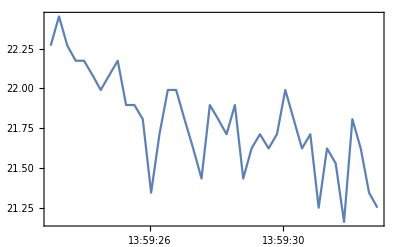

```mathematica
DateListPlot[data,PlotRange->All]
```

Close the device connection:

```mathematica
DeviceClose[sensor]
```

#### Advanced Usage

-Graphics-

Open the device:

```mathematica
sensor=DeviceOpen["Vernier"]
```

DeviceObject[…]

Schedule a task that takes one temperature reading every second:

```mathematica
RemoveScheduledTask/@ScheduledTasks[];
```

```mathematica
data={};

task=RunScheduledTask[
AppendTo[data,{Now,QuantityMagnitude@DeviceRead[sensor]}]
,1]
```

ScheduledTaskObject[…]

```mathematica
Dynamic[
DateListPlot[TimeSeries[data],
PlotRange->{0,All},
Filling->0]]
```

Remove the task and close the device:

```mathematica
RemoveScheduledTask[task];
DeviceClose[sensor];
```

### Science Experiments

In this section we are going to take a look at what happens when you take temperature readings of a liquid over a certain amount of time. For example, what happens to the temperature of a hot liquid in a room at “room temperature”. Or an ice cold liquid in the same room.

From experience, we know that hot liquids cool down and cold liquids warm up over time. In both cases they end up at “room temperature” after enough time has past. We apply this knowledge by waiting for a cup of hot tea or a bowl of soup to “cool down”. From our experience we know that hot tea in a room temperature environment does not get hotter over time.

#### Experiment #1 — Measuring the temperature of hot water over time

For this experiment you will need a Vernier temperature probe (both the Wide-Range and the Go!Temp should work for this experiment)

#### Newton’s Law Of Cooling

```mathematica
FormulaData["NewtonsLawOfCooling"]
```

dQ/dt Power==A Area h HeatTransferCoefficient (-T Temperature+T_2 Temperature)